```mathematica
SetDirectory[NotebookDirectory[]];
L=1;
T=1;
data=Import["anim.dat","Data"];
n=Dimensions[data]⟦2⟧;
k=Dimensions[data]⟦1⟧;
dx=Table[i*L/(n-1),{i,0,n-1}];
pic=Table[ListPlot[Table[{dx⟦i⟧,data⟦j⟧⟦i⟧},{i,1,n}],PlotRange->{{0,L},{-T,T}}],{j,1,k,1}];
Manipulate[Show[pic⟦j⟧],{j,1,k,1}]
```

```mathematica
Manipulate[Show[pic⟦j⟧],{j,1,k/10,1}]
```

```mathematica
(*Аналитическое решение теста 1*)
```

```mathematica
Manipulate[Plot[Sin[Pi*x]*Cos[Pi*t],{x,0,L},PlotRange->{{0,L},{-T,T}}],{t,0,T}]
```

General::prng: Value of option PlotRange -> {{0, L}, {-T, T}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value L in {x, 0, L} is not a machine-sized real number.

General::prng: Value of option PlotRange -> {{0, L}, {-T, T}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value L in {x, 0, L} is not a machine-sized real number.

```mathematica
(*Аналитическое решение теста 2*)
```

```mathematica
Eps=10^-4;
L=1;
T=1;
n=50;
k1=1/2(Sqrt[2/(Pi^2*Eps)]+1);
analitPic=Table[ListPlot[Table[{i*L/n,8/Pi^3 Sum[1/(2n1+1)^3 Sin[(2n1+1)*Pi*i*L/n]Cos[(2n1+1)*Pi*j*T/k],{n1,0,k1}]},{i,0,n}],PlotRange->{{0,L},{-T,T}}],{j,0,k}];
Manipulate[analitPic⟦j⟧,{j,1,k+1,1}]
```

Part::partd: Part specification analitPic ⟦ 1 ⟧ is longer than depth of object.

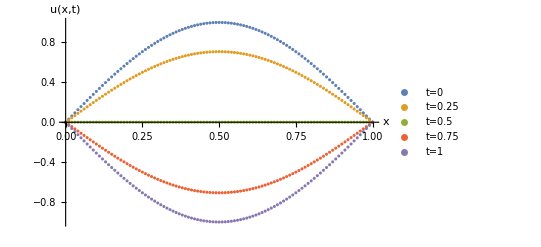

```mathematica
SetDirectory[NotebookDirectory[]];
data1=Import["SOLVE1.txt","Data"];
data2=Import["SOLVE2.txt","Data"];
data3=Import["SOLVE3.txt","Data"];
data4=Import["SOLVE4.txt","Data"];
data5=Import["SOLVE5.txt","Data"];
picall=Show[ListPlot[{data1,data2,data3,data4,data5},AxesLabel->(Style[#,12,Black,Italic]&/@{"x","u(x,t)"}),PlotLegends->{"t=0","t=0.25","t=0.5","t=0.75","t=1"}]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["All.pdf",picall];
```

```mathematica
j=0;
i=13;
data⟦j+1⟧⟦i+1⟧
Eps=10^-8;
L=1;
T=1;
k1=1/2(Sqrt[2/(Pi^2*Eps)]+1);
N[8/Pi^3 Sum[1/(2n1+1)^3 Sin[(2n1+1)*Pi*i*L/n]Cos[(2n1+1)*Pi*j*T/k],{n1,0,k1}]]
```

0.1131

0.112146